```mathematica
Clear[b,α, Δ, p, f, t,s,b];
f[α_,Δ_,p_] = 1/(8α(1-α(1+1/p+4/p^2+ Δ/2)))
```

1/(8 α (1-α (1+4/p^2+1/p+Δ/2)))

```mathematica
t[α_,Δ_,p_]= D[f[α,Δ,p], α]
```

-1/(8 α^2 (1-α (1+4/p^2+1/p+Δ/2)))-(-1-4/p^2-1/p-Δ/2)/(8 α (1-α (1+4/p^2+1/p+Δ/2))^2)

```mathematica
Reduce[D[t[α,Δ,p], α] >=0 && p > 0 && Δ>=0]
```

p>0&&Δ≥0&&0<α<(2 p^2)/(8+2 p+2 p^2+p^2 Δ)

```mathematica
b[Δ_, p_] =α/.Solve[t[α,Δ,p]==0,α][[1,1]]
```

p^2/(8+2 p+2 p^2+p^2 Δ)

```mathematica
b[Δ,p] < 1/(1+1/p+4/p^2+Δ/2)
```

p^2/(8+2 p+2 p^2+p^2 Δ)<1/(1+4/p^2+1/p+Δ/2)

```mathematica
Reduce[p^2/(8+2 p+2 p^2+p^2 Δ)<1/(1+4/p^2+1/p+Δ/2) && Δ>=0,p]
```

Δ≥0&&(p<0||p>0)

```mathematica
s[Δ_, p_] = f[b[Δ, p], Δ, p] //FullSimplify
```

(8+p (2+p (2+Δ)))/(4 p^2)

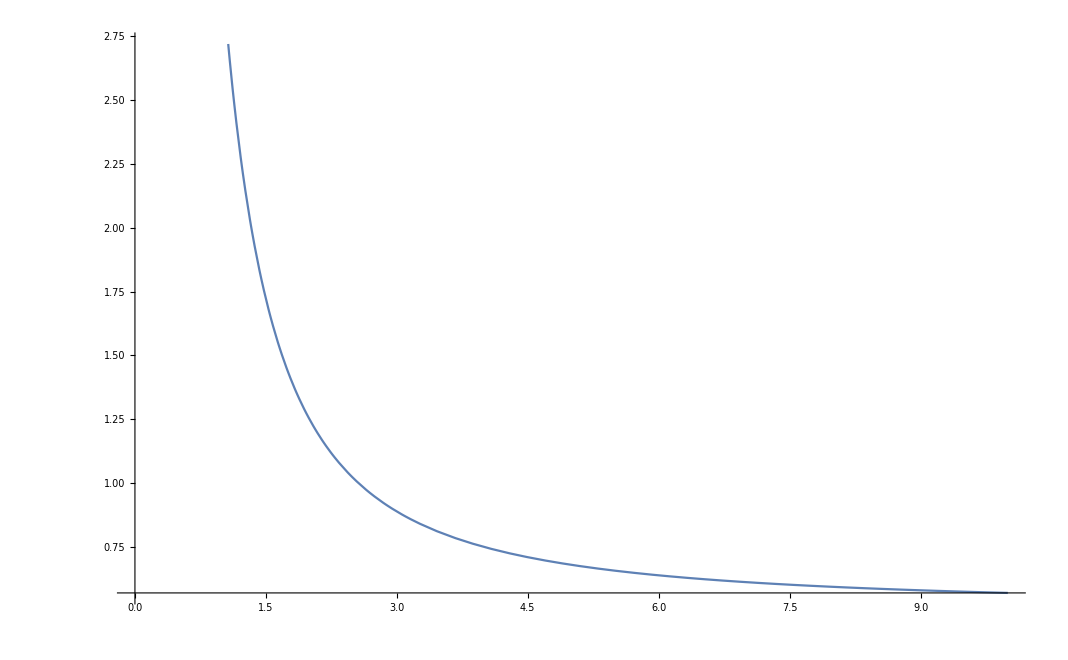

```mathematica
Plot[s[0.001,p],{p,0,10}]
```

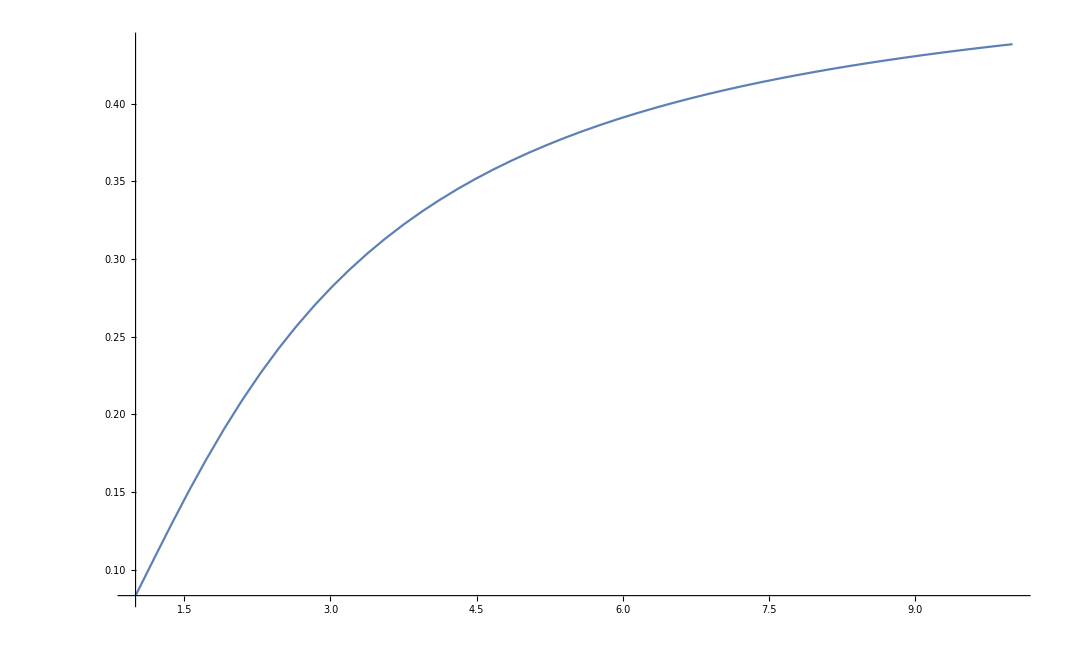

```mathematica
Plot[b[0.001,p],{p,1,10}]
```

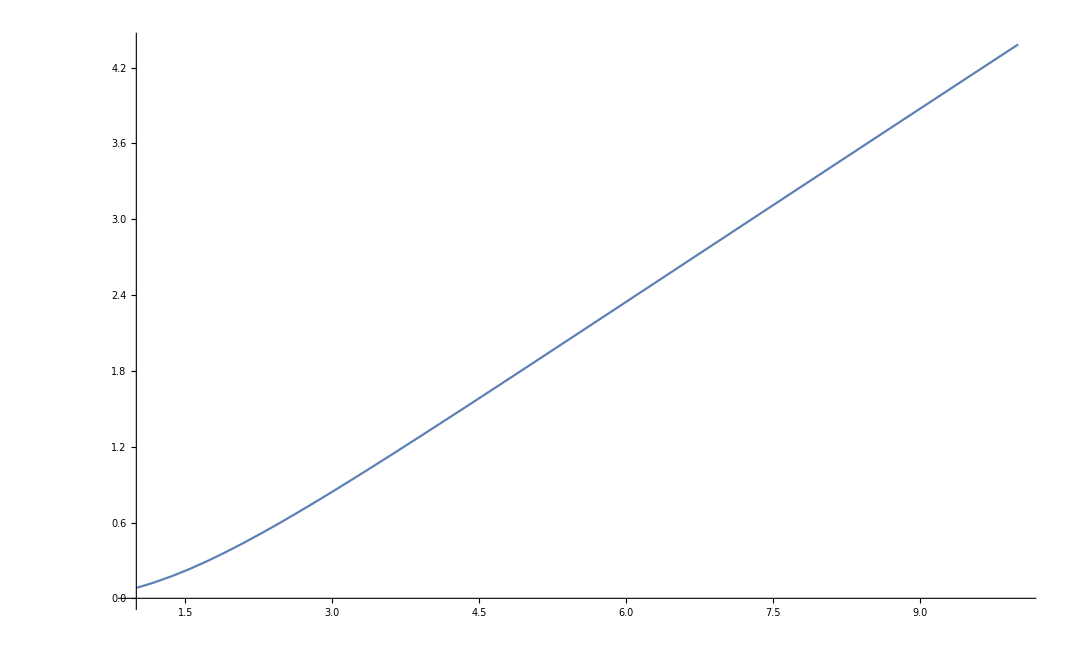

```mathematica
Plot[b[0.001,p]*p,{p,1,10}]
```

```mathematica
gain[Δ] = s[Δ,1]/Limit[s[Δ,p] \. Δ->aΔ,{Δ,p}->{1,+Infinity}] \. a ->Δ
```

```mathematica
gain[0]
```

6

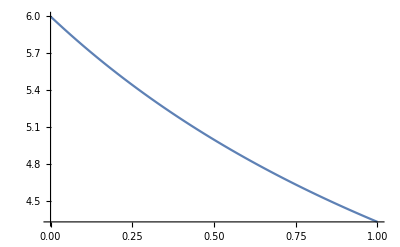

```mathematica
Plot[gain[Δ], {Δ,0,1}]
```